# CRSISF Fitting

## data loading

```mathematica
p0s={3.9,3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039,0.01,0.005,0.002,0.001,0.0005,0.00033,0.00014,0.000091,0.000077,0.000054,0.000045,0.000036},{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{999999, 999999, 999999,999999,46.2416,35.0693,135.321,564.239,829.48,897.484,1365.27,1522.57,3000},{ 999999, 999999, 999999,999999, 999999,60, 80, 200, 500, 800, 999999, 999999, 999999,999999, 999999, 999999, 999999},{ 999999, 999999, 999999,999999, 999999,25, 40 ,60, 80, 120,200 ,300 ,1000 ,999999, 999999,999999},{ 999999, 999999, 999999,999999, 999999,40 ,70 ,150 ,250, 600 ,2000, 999999 ,999999, 999999},{ 999999, 999999, 999999 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{ 999999, 999999, 999999,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
CRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]
],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeCRSISF_N4096_p3.9000_T0.00100000_waitingTime10000_idx17.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeCRSISF_N4096_p3.9000_T0.00100000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeCRSISF_N4096_p3.9000_T0.00050000_waitingTime10000_idx16.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
time=Table[Table[Table[Mean[DeleteCases[Table[CRSISF[[p,T,i,1,rec]],{i,Length[CRSISF[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRSISF[[p,T,i,1]]],{i,Length[CRSISF[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 640 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRSISFMean=Table[Table[Table[Mean[DeleteCases[Table[CRSISF[[p,T,i,2,rec]],{i,Length[CRSISF[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRSISF[[p,T,i,1]]],{i,Length[CRSISF[[p,T]]]}]]-1}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 114 of … does not exist.

Part::partw: Part 115 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
absTime=Table[Table[Table[time[[p,T,rec+1]]-time[[p,T,1]],{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

## What if we decompose α and β relaxations

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
LogStretchedExp[t_,G_,τ_,β_]:=G -(t/τ)^β;
```

```mathematica
αfitEndPos=Table[Table[Position[CRSISFMean[[p,i]],_?(#<0.5&)][[1,1]]+1,{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{82,120,139,165,53,59,64,74,79,81,86,88,90},{82,107,120,139,146,48,49,53,60,67,275,317,353,363,391,406,426},{70,82,88,107,120,41,43,44,45,47,48,49,51,186,197,209},{70,82,88,95,108,40,41,43,44,45,47,154,158,161},{89,95,101,38,39,40,41,42,42,42,43,43,43},{70,83,89,35,36,38,38,39,40,40,41}}

```mathematica
αfitStartPos=Table[Table[Position[CRSISFMean[[p,i]],_?(#<0.98&)][[1,1]]+1,{i,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{18,32,45,67,33,37,39,44,46,47,49,50,51},{17,26,32,45,52,28,29,33,37,39,121,137,148,153,162,168,174},{14,18,19,26,33,23,24,25,26,27,28,29,31,84,94,102},{14,18,19,21,26,22,23,24,25,26,27,58,61,65},{19,21,24,20,21,22,22,23,23,24,24,25,25},{14,18,19,18,19,20,21,21,22,22,22}}

```mathematica
α
```

```mathematica
αfitting=Table[Table[NonlinearModelFit[Table[{Normal[absTime[[p,T]][[rec]]],Log10[Normal[CRSISFMean[[p,T,rec]]]]},{rec,αfitStartPos[[p,T]],αfitEndPos[[p,T]]}],{LogStretchedExp[t,G,τ,B],{100000>τ>0.5,0.99>B>0.4,0>G}},{{τ,100},B,G},t,MaxIterations->Automatic],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

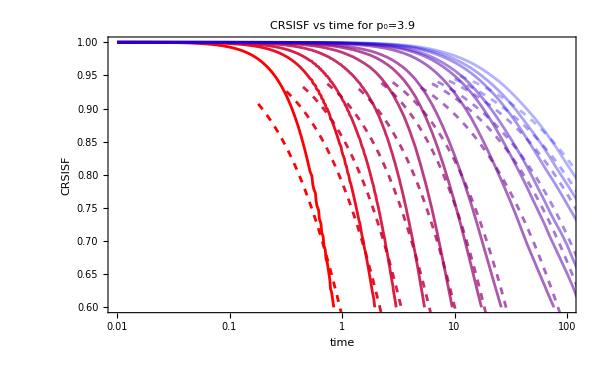
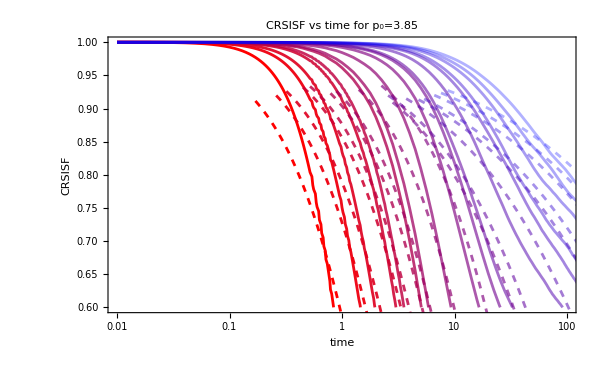
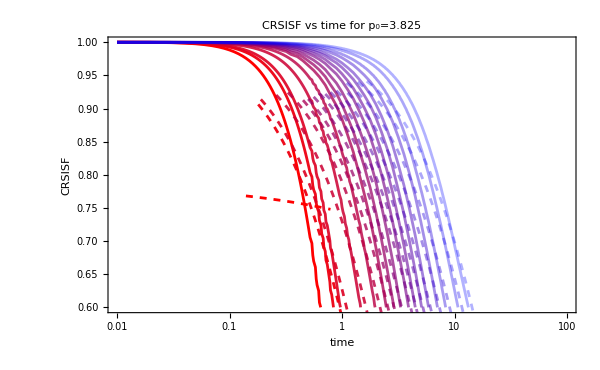
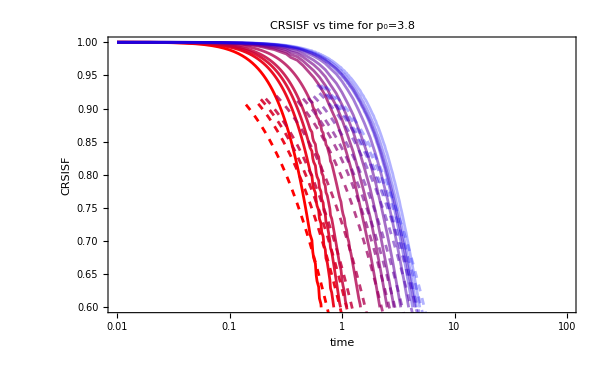
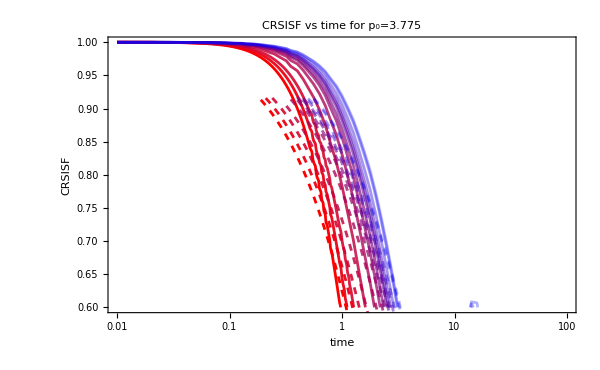
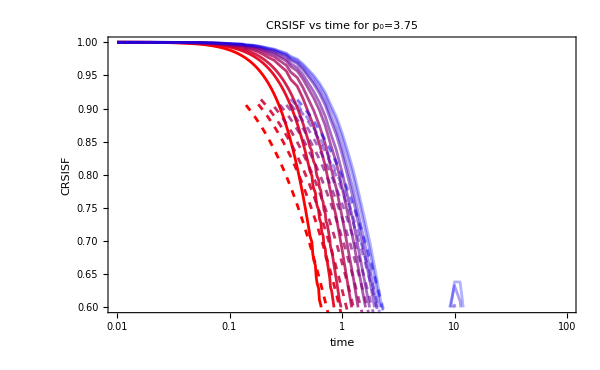

```mathematica
Table[Show[
ListLogLinearPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.01,100},{0.6,1}}],Table[LogLinearPlot[10^αfitting[[p,T]][x],{x,absTime[[p,T]][[αfitStartPos[[p,T]]]],absTime[[p,T]][[αfitEndPos[[p,T]]]]},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}]
```